```mathematica
f[x_,y_] =y
g[x_,y_] = -x + y(1 -x^2-y^2)
DF[x_,y_]={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};
DF[x,y]//MatrixForm
```

y

-x+y (1-x^2-y^2)

(0 | 1
-1-2 x y | 1-x^2-3 y^2)

```mathematica
pPlaneAnalysis[F_,G_,xRange_,yRange_]:=Module[{eqPts,eqPtsPlot,eVal,pplanePlot,xNullClinePlot,yNullClinePlot,esys,circlePlot,evPlots,EVPlot,limCyclePlot},
eqPts = Solve[{F==0,G==0},{x,y}];
For[j=1,j≤Length[eqPts],j++,
esys = Eigensystem[DF[x,y]/.eqPts[[j]]];
Subscript[evPlots, j]=ParametricPlot[esys[[2]]*s + Table[{x,y}/.eqPts[[j]] ,{k,1,2}],{s,-1,1},
PlotStyle->{Red, Thickness->.015},
RegionFunction->Function[{u,v,vx,vy,n},(((u-x)^2+(v -y)^2)/.eqPts[[j]])<.1]]];
EVPlot = Show[Table[Subscript[evPlots, j],{j,1,Length[eqPts]}]];
eqPtsPlot = ListPlot[{x,y}/.eqPts,
PlotMarkers->{Automatic,Large},
PlotStyle->Black];
pplanePlot = StreamPlot[{F,G},xRange,yRange];
xNullClinePlot = ContourPlot[F==0,xRange,yRange,ContourStyle->{Thickness[0.011],Red,Dashed}];

yNullClinePlot = ContourPlot[G==0,xRange,yRange,ContourStyle->{Thickness[0.011],Blue,Dashed}];
limCyclePlot=ParametricPlot[Evaluate[First[{x[t],y[t]} /. NDSolve[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],{x[0],y[0]}=={0,.8}},{x,y},{t,0,20}]]],{t,5,20},PlotStyle->{Orange,Thickness[0.011]}];
circlePlot=ParametricPlot[{2 Cos[t],2Sin[t]},{t,0,2Pi},PlotStyle->{Dashed,Thickness[0.011],Purple}];
Show[pplanePlot,eqPtsPlot,EVPlot,xNullClinePlot,yNullClinePlot,limCyclePlot,circlePlot,FrameLabel->{"x","y"}]
]
```

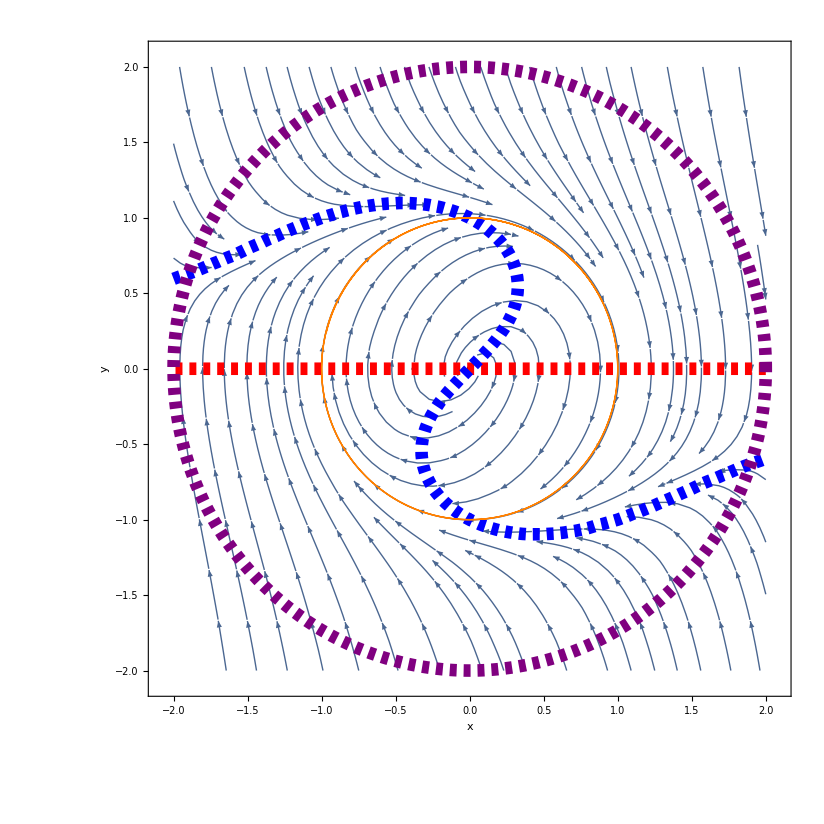

```mathematica
pp1=pPlaneAnalysis[f[x,y],g[x,y],{x,-2,2},{y,-2,2}]
```

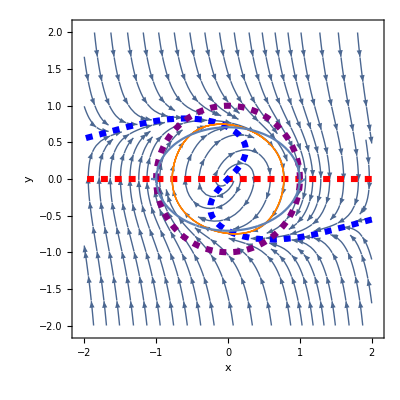

```mathematica
Show[pp1,ContourPlot[2x f[x,y] + 2y g[x,y]==0,{x,-2,2},{y,-2,2}]]
```